## Blunting neighborhoods + OAS constraint

```mathematica
everynbd1 = ContourPlot[Abs[y],{x,-2,2},{y,-2,2}, 
Contours->{2/2}, 
ContourShading->{{Yellow},{White}}, 
PlotPoints->100,
ContourStyle->None, 
Frame->False,
Axes->True,
Ticks->False,
AxesLabel->{Style["epitope 1",24,Black],Style["epitope 2",24,Black]}];
everynbd2 = ContourPlot[Abs[x],{x,-2,2},{y,-2,2},
 Contours->{2/2}, 
ContourShading->{{Cyan},{White}}, 
PlotPoints->100,
ContourStyle->None,
Frame->False,
Axes->True,
Ticks->False,
AxesLabel->{Style["epitope 1",24,Black],Style["epitope 2",24,Black]}];
anynbd = ContourPlot[UnitStep[2/2-Abs[x],2/2-Abs[y]],{x,-2,2},{y,-2,2}, 
Contours->{1},
PlotPoints->20,
ContourShading->{{White},{Green}},
ContourStyle->None,
Frame->False,
Axes->True,
Ticks->False,
AxesLabel->{Style["epitope 1",24,Black],Style["epitope 2",24,Black]}];
strainatorigin = Graphics[Disk[{0,0},.06]];
refpoint = Graphics[Style[Text[OverVector[p], {-.25,-.25}],FontSize->24]];
everyshow1 = Show[everynbd1,strainatorigin,refpoint, 
Graphics[Style[Text["β/2",{0.7,0.5}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0.2,1},{0.2,0}}]}],Graphics[Style[Text["(A)",{-1.75,1.75}],FontSize->24]],ImageSize->300];
everyshow2 = Show[everynbd2,strainatorigin,refpoint,
Graphics[Style[Text["β/2",{0.5,.45}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,0.13},{1,0.13}}]}],Graphics[Style[Text["(B)",{-1.75,1.75}],FontSize->24]],ImageSize->300];
anyshow = Show[anynbd,strainatorigin,refpoint,Graphics[Style[Text["β/2",{0.6,-0.6}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{-0.1,1},{-0.1,0}}]}],Graphics[Style[Text["β/2",{-0.6,.6}],FontSize->24]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,-0.1},{1,-0.1}}]}],
Graphics[Style[Text["(C)",{-1.75,1.75}],FontSize->24]],ImageSize->300];
everyshowcol = GraphicsColumn[{everyshow1, everyshow2}];
(*allnbds = GraphicsRow[{everyshowcol,Show[anyshow,ImageSize->Large]}]*)
gridorg = GraphicsGrid[{{everyshow1,anyshow, SpanFromLeft},{everyshow2,SpanFromAbove,SpanFromBoth}}];
toexport=Show[gridorg,ImageSize->900];
```

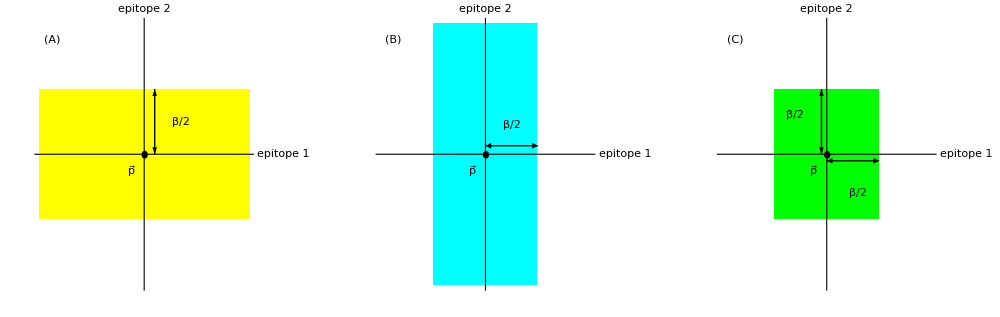

```mathematica
roworg = GraphicsRow[{everyshow1,everyshow2,anyshow}];
rowtoexport=Show[roworg,ImageSize->1000]
```